# Efficiency Comparison

## Defining Methods and Preamble

## Preamble

```mathematica
(*Set directory paths.*)
SetDirectory[NotebookDirectory[]];
```

## Plotting Method

```mathematica
hexColors={"#3f90da","#ffa90e","#bd1f01","#94a4a2","#832db6","#a96b59","#e76300","#b9ac70","#717581","#92dadd"};
RGBColor/@hexColors
makeBoxCMS[data_,labels_,yLabel_,cmsPos_,tevPos_,precY_:1,xLabelY_:0.06]:=Module[{majorLen,minorLen,makeTicks01,yVals,yTicks,yTicksRight,plot,cmsText,tevText,plotLeft=0.01,plotBottom=0.12,plotWidth=0.98,plotHeight=0.84,xCenters},majorLen=Scaled[0.015];
minorLen=Scaled[0.015/2];
makeTicks01[{vmin_?NumericQ,vmax_?NumericQ},prec_]:=Module[{maj,min},maj=N@FindDivisions[{vmin,vmax},6];
min=N@Flatten@Table[Most@Rest@Subdivide[maj[[k]],maj[[k+1]],6],{k,1,Length[maj]-1}];
Join[({#,NumberForm[#,{6,prec}],{majorLen,0}}&/@maj),({#,"",{minorLen,0}}&/@min)]];
yVals=Flatten[data];
yTicks=makeTicks01[{0,1.05 Max[yVals]},precY];
yTicksRight=yTicks/. {v_,_,len_}:>{v,"",len};


plot=BoxWhiskerChart[
data,
{"Basic",
{"MedianMarker",1.0,Directive[RGBColor["#b9ac70"],AbsoluteThickness[3]]},
{"Whiskers",Directive[Black,AbsoluteThickness[3]]},
{"Fences",0.5,Directive[Black,AbsoluteThickness[2]]},
{"MeanMarker",0.75,Directive[Black, Opacity[1],AbsoluteThickness[3]]},
{"MeanDiamond",0.8,Directive[Gray, Opacity[0.75]]}
(*{"Outliers",Directive[Black,AbsolutePointSize[5]]}*)
},
ChartStyle->Table[Directive[RGBColor["#3f90da"],Opacity[0.65]],{Length[data]}],
Frame->True,Axes->False,
FrameTicks->{{yTicks,yTicksRight},{Automatic,Automatic}},
FrameStyle->Directive[Black,AbsoluteThickness[2]],
FrameTicksStyle->Directive[Black,FontSize->22,FontFamily->"TeX Gyre Heros"],
LabelStyle->Directive[Black,FontSize->24,FontFamily->"TeX Gyre Heros"],
FrameLabel->{None,Style[yLabel,Black,FontSize->30,FontFamily->"TeX Gyre Heros"]},
GridLines->{None,Automatic},GridLinesStyle->Directive[GrayLevel[0.85], AbsoluteThickness[1.5]],
ImageSize->1300,AspectRatio->0.5,ImagePadding->{{100,40},{40,40}},PlotRange->{0,1.05 Max[yVals]},
PlotRangePadding->{{Scaled[-0.1],Scaled[0.02]},{Scaled[0.05],Scaled[0.01]}}
];

cmsText=Row[{Style["CMS",Bold,FontFamily->"TeX Gyre Heros",24],Style[" Simulation Preliminary",Italic,FontFamily->"TeX Gyre Heros",24]}];
tevText=Style["14 TeV",FontFamily->"TeX Gyre Heros",24];
xCenters={0.19, 0.36,0.535, 0.71};

Graphics[Join[{Inset[plot,Scaled[{plotLeft,plotBottom}],{Left,Bottom},Scaled[{plotWidth,plotHeight}]]},Table[Inset[Style[labels[[i]],FontFamily->"TeX Gyre Heros",22],Scaled[{xCenters[[i]],xLabelY}],{Center,Top}],{i,Length[labels]}],{Inset[cmsText,Scaled[cmsPos],{Left,Bottom}],Inset[tevText,Scaled[tevPos],{Right,Bottom}]}],PlotRange->{{0,1},{0,1}},AspectRatio->0.5,ImageSize->1300]]
```

{RGBColor[0.24705882352941178, 0.5647058823529412, 0.8549019607843137],RGBColor[1., 0.6627450980392157, 0.054901960784313725],RGBColor[0.7411764705882353, 0.12156862745098039, 0.00392156862745098],RGBColor[0.5803921568627451, 0.6431372549019608, 0.6352941176470588],RGBColor[0.5137254901960784, 0.17647058823529413, 0.7137254901960784],RGBColor[0.6627450980392157, 0.4196078431372549, 0.34901960784313724],RGBColor[0.9058823529411765, 0.38823529411764707, 0.],RGBColor[0.7254901960784313, 0.6745098039215687, 0.4392156862745098],RGBColor[0.44313725490196076, 0.4588235294117647, 0.5058823529411764],RGBColor[0.5725490196078431, 0.8549019607843137, 0.8666666666666667]}

## Data Plots

## Efficiency Plot: AE @ 250 Hz

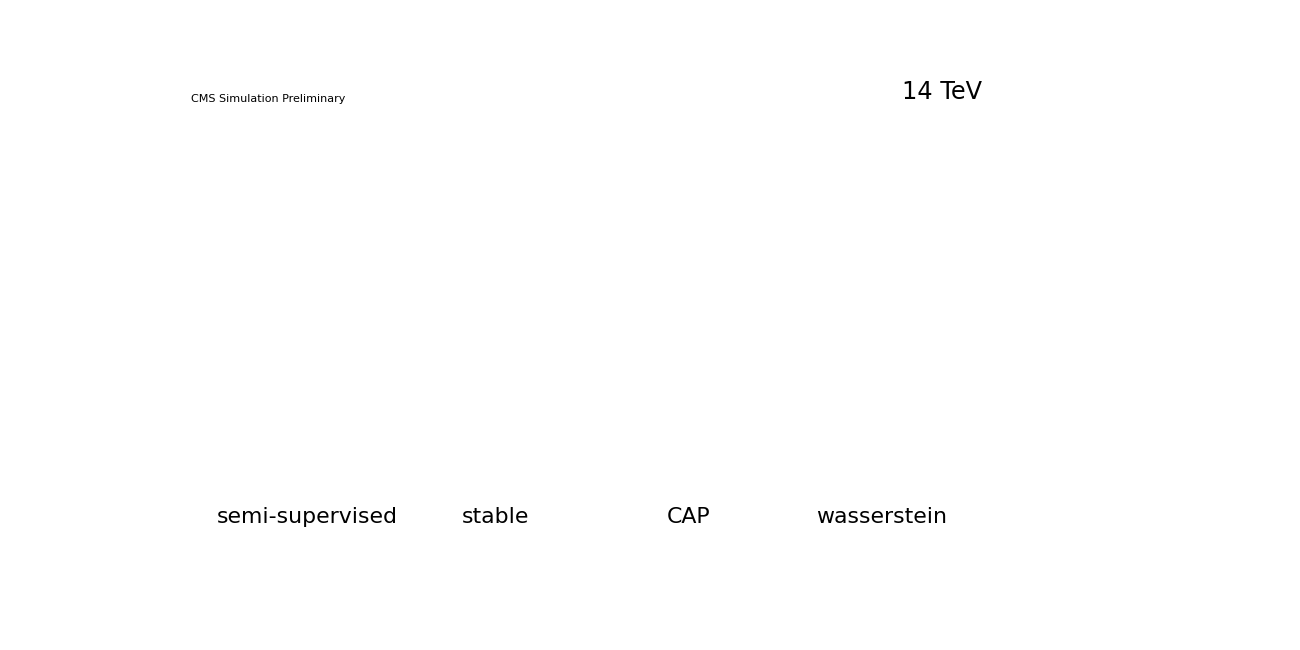

effs/ae_250Hz.svg

effs/ae_250Hz.pdf

effs/ae_250Hz.jpeg

```mathematica
(*Data*)
semisupervised={0.31,0.53,0.17,1.79,1.05,0.96,17.05,17.50,21.16,1.92,0.06,16.86,15.76,15.65,7.14,0.59,0.33,0.58,17.41};
CAP={0.37,0.50,0.00,0.11,0.82,0.77,0.87,12.45,13.10,17.47,0.69,0.04,13.59,11.89,10.17,3.29,0.29,0.27,0.44,13.87};
stable={0.19,0.34,0.00,0.04,0.72,0.70,0.79,9.78,9.97,16.11,0.57,0.03,12.87,9.84,8.82,2.60,0.24,0.39,0.74,12.38};
wasserstein={2.45,0.30,0.00,0.10,0.50,0.57,0.68,10.56,11.03,13.58,0.52,0.03,11.24,10.32,8.57,2.45,0.21,0.17,0.27,11.03};

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.8,0.9},1,0.17]
Export["effs/" <> "ae_250Hz" <>".svg",plot,"SVG"]
Export["effs/" <> "ae_250Hz" <>".pdf",plot,"PDF"]
Export["effs/" <> "ae_250Hz" <>".jpeg",plot,"JPEG"]
```

## Efficiency Plot: AE @ q99

```mathematica
(*Data*)
semisupervised={2.14,0.42,0.00,0.19,1.33,0.77,0.71,11.72,11.67,17.43,2.22,0.05,14.76,10.40,10.73,6.30,0.45,0.19,0.30,12.92};
CAP={0.22,0.22,0.00,0.03,0.73,0.57,0.67,5.12,5.31,14.36,0.42,0.02,12.12,5.78,5.01,1.92,0.22,0.17,0.29,9.91};
stable={2.77,0.31,0.00,0.13,0.66,0.54,0.64,10.36,10.56,12.88,0.57,0.03,10.84,9.93,8.67,2.62,0.27,0.20,0.32,10.44};
wasserstein={3.63,0.33,0.00,0.14,0.51,0.59,0.72,11.41,11.92,14.07,0.64,0.03,11.00,11.15,9.38,2.69,0.23,0.25,0.40,11.27};

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.8,0.9},1,0.17]
Export["effs/" <> "ae_q99" <>".svg",plot,"SVG"]
Export["effs/" <> "ae_q99" <>".pdf",plot,"PDF"]
Export["effs/" <> "ae_q99" <>".jpeg",plot,"JPEG"]
```

-Graphics-

effs/ae_q99.svg

effs/ae_q99.pdf

effs/ae_q99.jpeg

## Efficiency Plot: VAE @ 250 Hz

```mathematica
(*Data*)
semisupervised={0.03,0.15,0.00,0.01,0.94,0.84,0.98,6.96,7.25,18.19,0.51,0.03,14.22,7.93,7.32,2.32,0.32,0.37,0.65,13.44};
CAP={0.02,0.17,0.00,0.01,0.99,1.02,1.13,5.99,6.22,18.71,0.63,0.03,14.01,7.64,6.76,2.38,0.27,0.15,0.24,15.14};
stable={0.04,0.19,0.00,0.00,1.09,1.07,1.22,11.37,11.99,19.70,0.83,0.04,14.36,12.87,11.54,3.75,0.38,0.34,0.57,17.81};
wasserstein={0.05,0.19,0.00,0.00,1.00,0.96,1.09,9.38,9.69,19.87,0.65,0.04,15.25,10.63,9.09,2.81,0.36,0.45,0.84,15.60};

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.8,0.9},1,0.17]
Export["effs/" <> "vae_250Hz" <>".svg",plot,"SVG"]
Export["effs/" <> "vae_250Hz" <>".pdf",plot,"PDF"]
Export["effs/" <> "vae_250Hz" <>".jpeg",plot,"JPEG"]
```

-Graphics-

effs/vae_250Hz.svg

effs/vae_250Hz.pdf

effs/vae_250Hz.jpeg

```mathematica
Export["effs/" <> "vae_250Hz" <>".pdf",plot,"PDF"]
```

## Efficiency Plot: VAE @ q99

```mathematica
(*Data*)
semisupervised={0.21,0.15,0.00,0.02,0.93,0.72,0.85,6.24,6.38,17.24,0.52,0.03,13.26,6.55,6.46,2.22,0.31,0.41,0.77,11.64};
CAP={0.03,0.17,0.00,0.01,0.93,0.93,1.05,7.01,7.24,20.10,0.61,0.04,15.02,7.87,7.52,2.42,0.33,0.39,0.67,14.64};
stable={0.03,0.17,0.00,0.01,0.94,0.94,1.06,6.31,6.52,18.81,0.58,0.03,14.46,7.83,6.99,2.33,0.31,0.19,0.32,14.65};
wasserstein={0.02,0.19,0.00,0.01,1.04,1.12,1.25,7.52,7.80,20.99,0.73,0.04,15.11,9.46,8.16,2.79,0.33,0.16,0.25,17.29};

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.8,0.9},1,0.17]
Export["effs/" <> "vae_q99" <>".svg",plot,"SVG"]
Export["effs/" <> "vae_q99" <>".pdf",plot,"PDF"]
Export["effs/" <> "vae_q99" <>".jpeg",plot,"JPEG"]
```

-Graphics-

effs/vae_q99.svg

effs/vae_q99.pdf

effs/vae_q99.jpeg